## Optimisation of parameters in VQD

```mathematica
SetAttributes[GradDescent,HoldAll]
GradDescent[params_,objf_,conf_]:=Module[{cost,basecost,grad,paramst},
basecost=objf[params];
grad=Table[
paramst=params;
paramst[k]+=conf["dθ"];
(objf[paramst]-basecost)/conf["dθ"] 
,{k,Keys@params}];
grad=grad/Max[Norm[grad,2],10^-10]
]

SetAttributes[NatGrad,HoldAll]
NatGrad[params_,objf_,conf_]:=Module[{cost,mρ},
cost=objf[params];
mρ=GetQuregMatrix[];
];


SetAttributes[UpdateCost,HoldAll]
UpdateCost[params_,objf_,conf_]:=Module[{grad, beststep,gradstep,tparams,cbest,cnew},
beststep=conf["gradstep"];
gradstep=beststep;
grad=GradDescent[params,objf,conf];

tparams=Normal@params;
tparams[[All,2]]-=conf["gradstep"]*grad;
cbest=objf[tparams];
If[NumberQ[conf["gradstepmultiply"]],

While[True,
gradstep*=conf["gradstepmultiply"];
tparams=Normal@params;
tparams[[All,2]]-=gradstep*grad;
cnew=objf[tparams];

If[cnew>=cbest, Break[]];
cbest=cnew;
beststep=gradstep
];
];
tparams=Normal@params;
tparams[[All,2]]-=beststep*grad;
params=Association@tparams;
cbest
]

ParamsFit::usage="ParamsFit[device, conf]. Parameterisation fitting.";
SetAttributes[ParamsFit,HoldAll]
ParamsFit[params_,objf_,conf_]:=Module[{cost, iter,dcost,oldcost,oldparams,paramsinit,converge=0,costlist={},costinit},
iter=0;
cost=objf[params];
costinit=cost;paramsinit=params;
AppendTo[costlist,cost];
Monitor[
While[True,
oldcost=cost;
oldparams=params;
cost=UpdateCost[params,objf,conf];

dcost=cost-oldcost;
If[dcost>=0&&iter>1,
(*revert to old cond*)
{cost,params}={oldcost,oldparams};
Break[]
];

If[cost<=conf["costfin"],
Break[]
];

If[(++iter> conf["maxiter"])||converge>=conf["convergenum"],
Break[]];

AppendTo[costlist,cost];
];
,Column@{"cost="<>ToString@cost,"iter="<>ToString@iter}];

If[cost>=costinit,
Print["Optimisation have failed, use the initial parameter guess"];
{cost,params}={costinit,paramsinit}
];

AppendTo[costlist,cost];
Print[ListPlot[costlist]];
{objf[params],params}
]
```

## Fitting the Bell state

```mathematica
ρmat=RandomMixState[6];
```

```mathematica
bellcircρ=<|"01"->{Subscript[Rx, 0][π/2],Subscript[Rx, 1][-π/2],Subscript[C, 0][Subscript[Z, 1]],Subscript[Rx, 1][π/2]},"12"->{Subscript[Rx, 1][π/2],Subscript[Rx, 2][π/2],Subscript[C, 1][Subscript[Z, 2]],Subscript[Rx, 2][π/2]},"23"->{Subscript[Rx, 2][π/2],Subscript[Rx, 3][π/2],Subscript[C, 2][Subscript[Z, 3]],Subscript[Rx, 3][π/2]},"34"->{Subscript[Rx, 3][π/2],Subscript[Rx, 4][π/2],Subscript[C, 3][Subscript[Z, 4]],Subscript[Rx, 4][π/2]},"45"->{Subscript[Rx, 4][π/2],Subscript[Rx, 5][-π/2],Subscript[C, 4][Subscript[Z, 5]],Subscript[Rx, 5][-π/2]}|>;
bellcircψ=<|"01"->{Subscript[X, 0],Subscript[Rx, 0][π/2],Subscript[Rx, 1][-π/2],Subscript[C, 0][Subscript[Z, 1]],Subscript[Rx, 1][π/2]},"12"->{Subscript[Rx, 0][π/2],Subscript[Rx, 1][π/2],Subscript[C, 0][Subscript[Z, 1]],Subscript[Rx, 1][π/2]},"23"->{Subscript[Rx, 0][π/2],Subscript[Rx, 1][π/2],Subscript[C, 0][Subscript[Z, 1]],Subscript[Rx, 1][π/2]},"34"->{Subscript[Rx, 0][π/2],Subscript[Rx, 1][π/2],Subscript[C, 0][Subscript[Z, 1]],Subscript[Rx, 1][π/2]},"45"->{Subscript[X, 1],Subscript[Rx, 0][π/2],Subscript[Rx, 1][-π/2],Subscript[C, 0][Subscript[Z, 1]],Subscript[Rx, 1][-π/2]}|>;
DestroyAllQuregs[];
ρ=CreateDensityQureg[6];
ρ2=CreateDensityQureg[2];
ψ=CreateQureg[6];
ψ2=CreateQureg[2];

bellcost[params_]:=Module[{init={},qubits,plot,codes,fidtarget,opt,wrap},
codes=ReplaceList[Sort@Range[0,5],{p___,a_,b_,q___}:>StringRiffle[{a,b},""]];
fidtarget=<|"01"->89.2,"12"->90.1,"23"->88.3,"34"->95.6,"45"->94.1|>;
wrap[θ_]:=If[θ>1,1,θ];
Mean@Table[
qubits=ToExpression@StringSplit[code,""];
If[Length@Intersection[qubits,{0,1,2}]>0,AppendTo[init,Subscript[Init, 0,1,2]]];
If[Length@Intersection[qubits,{3,4,5}]>0,AppendTo[init,Subscript[Init, 3,4,5]]];
SetQuregMatrix[ρ,ρmat];
opt={FidCZ-><|0->Subscript[θ, 0],1->Subscript[θ, 1],2->Subscript[θ, 2],3->Subscript[θ, 3],4->Subscript[θ, 4]|>,EFSingleXY->{Subscript[θ, 5],1-Subscript[θ, 5]}}/.params;
ApplyCircuit[ρ,ExtractCircuit@InsertCircuitNoise[SerializeCircuit@Flatten@{init,bellcircρ[code]},SiliconDelft[Sequence@@opt]]];
SetQuregMatrix[ρ2,PartialTrace[ρ,Sequence@@Complement[Range[0,5],qubits]]];
ApplyCircuit[InitZeroState@ψ2,bellcircψ[code]];
Abs[CalcFidelity[ρ2,ψ2]-0.01*fidtarget[code]]
,{code,codes}]
]
```

```mathematica
params=<|Subscript[θ, 0]->0.928,Subscript[θ, 1]->0.93,Subscript[θ, 2]->0.92,Subscript[θ, 3]->0.986,Subscript[θ, 4]->0.97,Subscript[θ, 5]->0.8|>;
conf=<|
"nqubits"->6,
"maxiter"->10000,
"gradstep"->0.0001,
"gradstepmultiply"->False,
(* delta params *)
"dθ"->10^-8,
"convergenum"->10,
"costfin"->10^-7
|>;
```

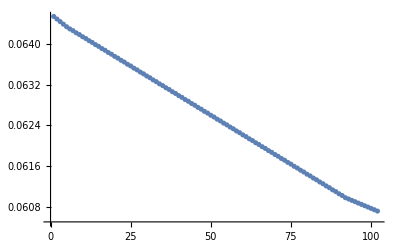

{0.0607218,<|θ_0→0.927758,θ_1→0.92551,θ_2→0.922819,θ_3→0.990573,θ_4→0.965064,θ_5→0.79999|>}

```mathematica
{cost,params}=ParamsFit[params,bellcost,conf]
```

```mathematica
fids[params_]:=Module[{init={},qubits,plot,codes,fidtarget,opt,wrap},
codes=ReplaceList[Sort@Range[0,5],{p___,a_,b_,q___}:>StringRiffle[{a,b},""]];
fidtarget=<|"01"->89.2,"12"->90.1,"23"->88.3,"34"->95.6,"45"->94.1|>;
wrap[θ_]:=θ;
Table[
qubits=ToExpression@StringSplit[code,""];
If[Length@Intersection[qubits,{0,1,2}]>0,AppendTo[init,Subscript[Init, 0,1,2]]];
If[Length@Intersection[qubits,{3,4,5}]>0,AppendTo[init,Subscript[Init, 3,4,5]]];
SetQuregMatrix[ρ,RandomMixState[6]];
opt={FidCZ->wrap[<|0->Subscript[θ, 0],1->Subscript[θ, 1],2->Subscript[θ, 2],3->Subscript[θ, 3],4->Subscript[θ, 4]|>/.params],EFSingleXY->{wrap@Subscript[θ, 5],1-wrap@Subscript[θ, 5]}};
ApplyCircuit[ρ,ExtractCircuit@InsertCircuitNoise[SerializeCircuit@Flatten@{init,bellcircρ[code]},SiliconDelft[Sequence@@opt]]];
SetQuregMatrix[ρ2,PartialTrace[ρ,Sequence@@Complement[Range[0,5],qubits]]];
ApplyCircuit[InitZeroState@ψ2,bellcircψ[code]];
CalcFidelity[ρ2,ψ2]
,{code,codes}]
]
```

```mathematica
wrap[θ_NumberQ]:=If[θ>1,1,θ];
opt={FidCZ->wrap[<|0->Subscript[θ, 0],1->Subscript[θ, 1],2->Subscript[θ, 2],3->Subscript[θ, 3],4->Subscript[θ, 4]|>/.params],EFSingleXY->{wrap@Subscript[θ, 5],1-wrap@Subscript[θ, 5]}/.params}
```

{FidCZ→If[<|0→0.928,1→0.93,2→0.92,3→0.986,4→0.97|>>1,1,<|0→0.928,1→0.93,2→0.92,3→0.986,4→0.97|>],EFSingleXY→{0.8,0.2}}

```mathematica
fids[params]
```

{0.891181,0.907212,0.61533,0.917015,0.948718}